# Lab #3

## Discrete-time logistic exploration

Here we will further explore the discrete logistic equation discussed in class and in May (1974): n[t+1]=n[t]exp[r*(1-n[t]/k)].

#### Simulate the difference equation for r=1.0,1.4,1.8,2.2,2.6,3.0.

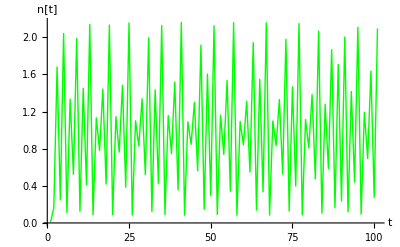

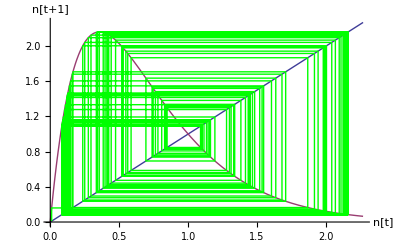

```mathematica
Clear[n,f];

(* set parameters *)

r=2.8;
n[0]=0.01;
tmax=100;
f[n_]:=n*E^(r*(1-n));

(* iterate difference equation *)

Do[
	n[t+1]=f[n[t]];
	,{t,0,tmax}];

(* plot n[t] as a function of t *)

ListPlot[Table[n[t],{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->RGBColor[0,1,0],AxesLabel->{"t","n[t]"}]

(* illustrate "cobwebbing" -- don't worry about the details of this code *)

Show[Plot[{n,f[n]},{n,0,1.05*E^(r-1)/r},DisplayFunction->Identity],
  Graphics[{RGBColor[0,1,0],Line[Flatten[Table[{{n[t],n[t]},{n[t],n[t+1]}},{t,0,tmax}],1]]}],
  PlotRange->{{0,1.05*E^(r-1)/r},{0,1.05*E^(r-1)/r}},AxesLabel->{"n[t]","n[t+1]"}]
```

#### At what value of r do 2-cycles begin? Investiagate the transition between a stable equilibrium and a 2-cycle by slowly raising r through this critical value. Simulate the model (ie, copy the above code and paste it down here) and also plot n[t+2] vs n[t] to see the birth of the 2-cycle using the code below. Between 1.96 and 1.97 is when the 2 cycles begin

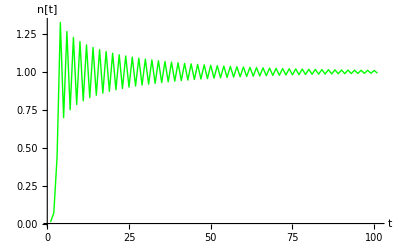

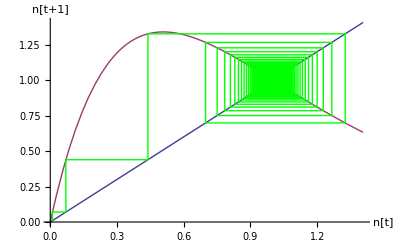

```mathematica
Clear[n,f];

(* set parameters *)

r=1.97;
n[0]=0.01;
tmax=100;
f[n_]:=n*E^(r*(1-n));

(* iterate difference equation *)

Do[
	n[t+1]=f[n[t]];
	,{t,0,tmax}];

(* plot n[t] as a function of t *)

ListPlot[Table[n[t],{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->RGBColor[0,1,0],AxesLabel->{"t","n[t]"}]

(* illustrate "cobwebbing" -- don't worry about the details of this code *)

Show[Plot[{n,f[n]},{n,0,1.05*E^(r-1)/r},DisplayFunction->Identity],
  Graphics[{RGBColor[0,1,0],Line[Flatten[Table[{{n[t],n[t]},{n[t],n[t+1]}},{t,0,tmax}],1]]}],
  PlotRange->{{0,1.05*E^(r-1)/r},{0,1.05*E^(r-1)/r}},AxesLabel->{"n[t]","n[t+1]"}]
```

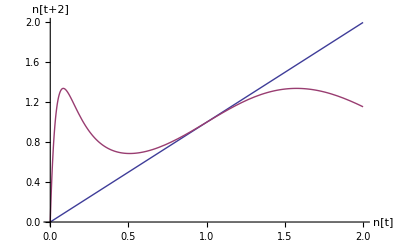

```mathematica
Plot[{n,f[f[n]]},{n,0,2},PlotRange->{0,2},AxesLabel->{"n[t]","n[t+2]"}]
```

#### Investiagate the transition between a 2-cycle and a 4-cycle by slowly raising r through r=2.526. Simulate the model and also plot n[t+4] vs n[t] using the code below.

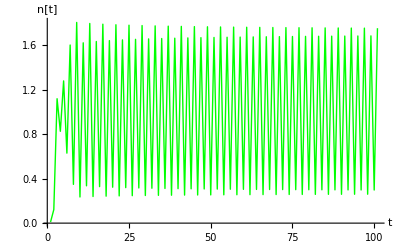

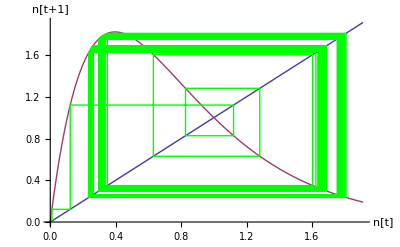

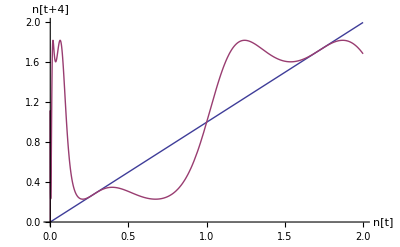

```mathematica
Clear[n,f];

(* set parameters *)

r=2.526;
n[0]=0.01;
tmax=100;
f[n_]:=n*E^(r*(1-n));

(* iterate difference equation *)

Do[
	n[t+1]=f[n[t]];
	,{t,0,tmax}];

(* plot n[t] as a function of t *)

ListPlot[Table[n[t],{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->RGBColor[0,1,0],AxesLabel->{"t","n[t]"}]

(* illustrate "cobwebbing" -- don't worry about the details of this code *)

Show[Plot[{n,f[n]},{n,0,1.05*E^(r-1)/r},DisplayFunction->Identity],
  Graphics[{RGBColor[0,1,0],Line[Flatten[Table[{{n[t],n[t]},{n[t],n[t+1]}},{t,0,tmax}],1]]}],
  PlotRange->{{0,1.05*E^(r-1)/r},{0,1.05*E^(r-1)/r}},AxesLabel->{"n[t]","n[t+1]"}]

Plot[{n,f[f[f[f[n]]]]},{n,0,2},PlotRange->{0,2},AxesLabel->{"n[t]","n[t+4]"}]
```

#### One hallmark of chaos is "sensitive dependence on inital conditions". This means that if you run two copies of the exact same equation with slightly different initial densities, the two diverge over time. Demonstrate sensitive dependence on initial conditions for r=3.0, and the lack of it for r=2.6 by simultaneously solving two identical difference equations with slightly different initial conditions, then plotting the difference between the solutions. Why do chaotic populations diverge then converge again? They diverge because they are chaotic and any initial difference will follow a different path than another initial density amount. However, the population dynamics are bounded and so by pure luck they will occasionally come back to similar numbers.

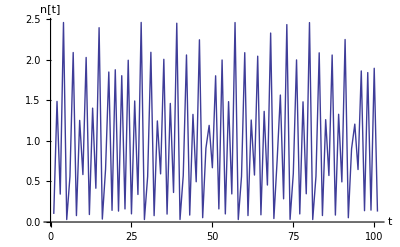

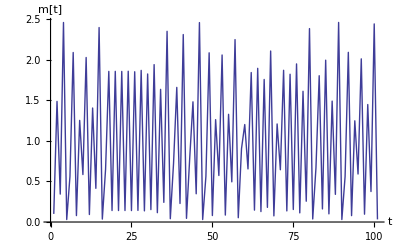

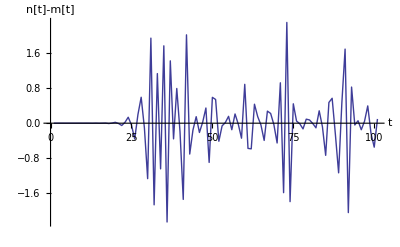

```mathematica
Clear[n,f];

(* set parameters *)

r=3.0;
n[0]=0.1;
m[0]=0.10001;
tmax=100;
f[n_]=n*E^(r*(1-n));

(* iterate difference equation *)

Do[
n[t+1]=f[n[t]];
m[t+1]=f[m[t]];
	,{t,0,tmax}];

(* plot n[t], m[t], and n[t]-m[t] as a function of t *)

ListPlot[Table[n[t],{t,0,tmax}],Joined->True,AxesLabel->{"t","n[t]"}]
ListPlot[Table[m[t],{t,0,tmax}],Joined->True,AxesLabel->{"t","m[t]"}]
ListPlot[Table[n[t]-m[t],{t,0,tmax}],Joined->True,AxesLabel->{"t","n[t]-m[t]"}]
```

#### A bifurcation diagram is a convenient summary of how a model depends on its parameters. Make one for the discrete logistic map, plotting the population densities reached as a function of r.

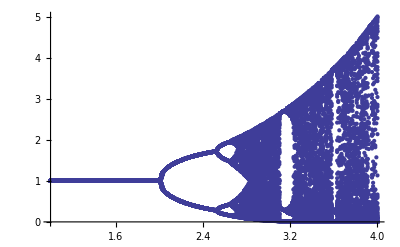

```mathematica
tmax=200;

(* solve the difference equation for values of r between 0 and 4 stepping by 0.01 *)

Do[
	   n[0,r]=1.01;
     Do[
	        n[t+1,r]=n[t,r]*E^(r*(1-n[t,r]));
	 ,{t,0,tmax}];
,{r,1.0,4.0,0.01}]

(* plot the final 100 points for each r *)

ListPlot[Flatten[Table[{r,n[t,r]},{r,1.0,4.0,0.01},{t,tmax-100,tmax}],1]]
```

#### Notice the "windows" in the chaotic region, such as the one around r=3.12. What type of solution is occurs for this range of r? Simulate the difference equation and see. What happens as r increases? Note: the cobwebbing code below plots only the last 30 years of data to eliminate the transient dynamics that would obscure the long-term behavior. The solution that occurs is that the population has two-point cycle, with one of the points being zero or very close to it. As r increases, the system gets chaotic again.

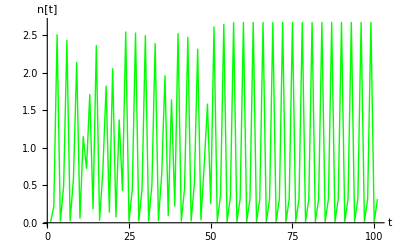

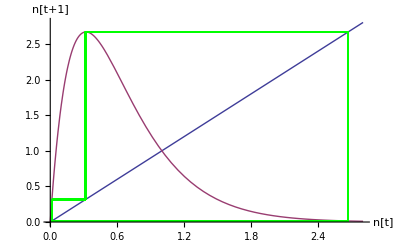

```mathematica
Clear[n,f];

(* set parameters *)

r=3.12;
n[0]=0.01;
tmax=100;
f[n_]:=n*E^(r*(1-n));

(* iterate difference equation *)

Do[
	n[t+1]=f[n[t]];
	,{t,0,tmax}];

(* plot n[t] as a function of t *)

ListPlot[Table[n[t],{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->RGBColor[0,1,0],AxesLabel->{"t","n[t]"}]

(* illustrate "cobwebbing" -- don't worry about the details of this code *)

Show[Plot[{n,f[n]},{n,0,1.05*E^(r-1)/r},DisplayFunction->Identity],
  Graphics[{RGBColor[0,1,0],Line[Flatten[Table[{{n[t],n[t]},{n[t],n[t+1]}},{t,tmax-30,tmax}],1]]}],
  PlotRange->{{0,1.05*E^(r-1)/r},{0,1.05*E^(r-1)/r}},AxesLabel->{"n[t]","n[t+1]"}]
```

### Be sure to run the following line!!

```mathematica
Needs["BarCharts`"]
```

## Understanding eigenvectors

```mathematica
a={{0.1,0.8},{0.7,0.6}};
k=2; (* dimension a *)
```

### Calculate the eigenvaluse and eigenvectors of a. Will the population grow or not? What do you predict the stable age distribution to be?

```mathematica
Eigenvalues[a]
```

```mathematica
{1.138986691902975  ,-0.4389866919029749}
```

```mathematica
Eigenvectors[a]
```

{{-0.610084,-0.792337},{-0.829335,0.558751}}

The population will grow because the dominant eigenvalue is above 1. The stable age distribution is the eigenvector corresponding to the dominant eigenvalue, which is {-0.610084,-0.792337}.

```mathematica
.792337/.610084
```

1.29873

### Project the population 10 years into the future. Were your expectations correct?

It grew!  Yay!  Our expectations were awesome.  The stable age distribution calls for a ratio of 1.29 of the second group for every 1 of the first group, and the bar graph looks to be approaching that ratio.

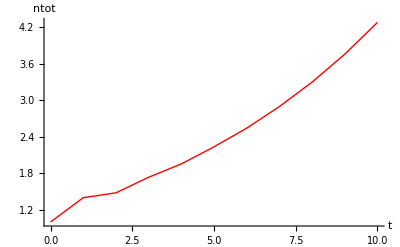

```mathematica
tmax=10;
n[0]={0,1};

Do[
ntot[t]=Sum[n[t][[i]],{i,1,k}];
n[t+1]=a.n[t];
,{t,0,tmax}];

ListPlot[Table[{t,ntot[t]},{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{"t","ntot"}]

Animate[BarChart[n[t],PlotLabel->t],{t,0,tmax,1},AnimationRunning->False]
```

### Now plot the dynamics in the n1-n2 phase plane along with the eigenvectors. Can you see how eigenvectors affect the dynamics? What is the meaning of the dominant AND other eigenvalue?

The right eigenvector gives the stable age distribution as seen by how the red line is collapsing onto the positively sloped line.  The left eigenvector gives the reproductive value as seen by the negatively sloped line.  The dominant eigenvalue gives the reproductive rate.  The other eigenvalue determines the transient dynamics of the population.

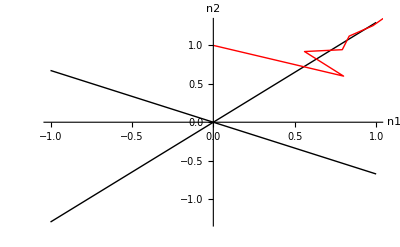

```mathematica
evplot=Plot[{x*Eigenvectors[a][[1,2]]/Eigenvectors[a][[1,1]],x*Eigenvectors[a][[2,2]]/Eigenvectors[a][[2,1]]},{x,-1,1},PlotStyle->Black];
dynplot=ListPlot[Table[n[t],{t,0,tmax}],Joined->True,PlotStyle->Red];
Show[evplot,dynplot,AxesLabel->{n1,n2}]
```

## US Population Growth

### Here is a Leslie matrix for the US population in 1966, divided into 10 5-year age classes (0-5, 5-10, 10-15, ..., 45-50). It projects the population from time t to time t+5.

```mathematica
(* US population, 1966, 5 year age classes *)

a={{0,0.00102,0.08515,0.30574,0.40002,0.28061,0.15260,0.06420,0.01483,0.00089},{0.99670,0,0,0,0,0,0,0,0,0},{0,0.99837,0,0,0,0,0,0,0,0},{0,0,0.99780,0,0,0,0,0,0,0},{0,0,0,0.99672,0,0,0,0,0,0},{0,0,0,0,0.99607,0,0,0,0,0},{0,0,0,0,0,0.99472,0,0,0,0},{0,0,0,0,0,0,0.99240,0,0,0},{0,0,0,0,0,0,0,0.98867,0,0},{0,0,0,0,0,0,0,0,0.98274,0}};
k=Length[a];
```

```mathematica
a//MatrixForm
```

(0 | 0.00102 | 0.08515 | 0.30574 | 0.40002 | 0.28061 | 0.1526 | 0.0642 | 0.01483 | 0.00089
0.9967 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.99837 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.9978 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.99672 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.99607 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.99472 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.9924 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.98867 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.98274 | 0)

### Find the eigenvalues and set λ to the dominant eigenvalue. Is the population growing or shrinking?

The population is growing because lambda is greater than one.

```mathematica
Eigenvalues[a]
```

{1.04975,0.311195+0.744209 ⅈ,0.311195-0.744209 ⅈ,-0.393884+0.365782 ⅈ,-0.393884-0.365782 ⅈ,0.0115489+0.522137 ⅈ,0.0115489-0.522137 ⅈ,-0.411157+0.120416 ⅈ,-0.411157-0.120416 ⅈ,-0.0851577}

```mathematica
λ=Eigenvalues[a][[1]]
```

1.04975

### Find w, the right eigenvector associated with the dominant eigenvalue. This gives the stable age distribution.

```mathematica
w=Eigenvectors[a][[1]]
```

{0.391303,0.371527,0.353342,0.335854,0.318887,0.30258,0.286717,0.271052,0.25528,0.238984}

### Find v, the left eigenvector associated with the dominant eigenvalue. This gives the reproductive value of each stage. (If this turns out negative, multiply by -1...). What individuals of which stage contribute most to future generations?

The third stage contributes the most to the future generations as it has the highest value.

```mathematica
v=-Eigenvectors[Transpose[a]][[1]]
```

{0.427932,0.450711,0.47347,0.461604,0.354898,0.202168,0.0926338,0.0321847,0.0063851,0.000362809}

### Simulate the population over 40 time steps (=200 years). Initial population vector = 1 in first age class, no one else. (This doesn't produce output yet).

```mathematica
tmax=40;
n[0]=Table[If[i==1,1,0],{i,1,k}];

Do[
ntot[t]=Sum[n[t][[i]],{i,1,k}];
n[t+1]=a.n[t];
,{t,0,tmax}];
```

### Plot total population size vs time. Does population grow at a constant rate?

No, it does not grow at a constant rate because it is not linear.

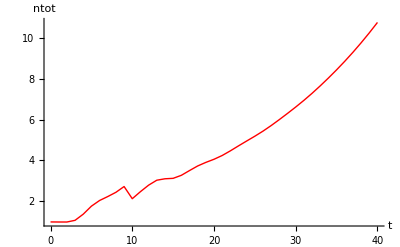

```mathematica
ListPlot[Table[{t,ntot[t]},{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{"t","ntot"}]
```

### Now plot the age distribution over time. Explain the dynamics.

There is an initial group of individuals that must reach sexual maturity before producing another group of stage 1 individuals. This initial group then continues to produce stage 1 individuals as the other groups grow, eventually leading to a stable age distribution. In the eventual stable age distribution, stage 1 has the most individuals, while stage 10 has the least, with a linear decline between the extreme stages.

```mathematica
Animate[BarChart[n[t],PlotLabel->t],{t,0,tmax,1},AnimationRunning->False]
```

### Calculate the sensitivity matrix. Each entry is the sensitivity of λ to the corresponding entry in the Lefkovitch/Leslie matrix. What transition rate/probability is λ most sensitive to? Can this transition actually change?

The most sensitive entry is the first column, third row, with .213304. This cell corresponds to the probability of babies being born as 5-10 year olds, which is not possible, and so this cell could not actually change.

```mathematica
s=Outer[Times,v,w]/v.w;
s//MatrixForm
```

(0.192788 | 0.183045 | 0.174085 | 0.16547 | 0.15711 | 0.149076 | 0.141261 | 0.133543 | 0.125772 | 0.117743
0.20305 | 0.192788 | 0.183352 | 0.174278 | 0.165473 | 0.157011 | 0.14878 | 0.140651 | 0.132467 | 0.124011
0.213304 | 0.202524 | 0.19261 | 0.183078 | 0.173829 | 0.16494 | 0.156293 | 0.147754 | 0.139156 | 0.130273
0.207958 | 0.197448 | 0.187783 | 0.17849 | 0.169472 | 0.160806 | 0.152376 | 0.144051 | 0.135669 | 0.127008
0.159886 | 0.151805 | 0.144375 | 0.137229 | 0.130297 | 0.123633 | 0.117152 | 0.110751 | 0.104307 | 0.0976484
0.0910791 | 0.0864761 | 0.0822433 | 0.078173 | 0.0742237 | 0.070428 | 0.0667358 | 0.0630897 | 0.0594187 | 0.0556256
0.0417326 | 0.0396235 | 0.037684 | 0.035819 | 0.0340094 | 0.0322702 | 0.0305785 | 0.0289078 | 0.0272257 | 0.0254877
0.0144996 | 0.0137668 | 0.0130929 | 0.012445 | 0.0118162 | 0.011212 | 0.0106242 | 0.0100437 | 0.00945932 | 0.00885546
0.00287656 | 0.00273118 | 0.0025975 | 0.00246895 | 0.00234422 | 0.00222434 | 0.00210773 | 0.00199257 | 0.00187663 | 0.00175683
0.000163449 | 0.000155189 | 0.000147593 | 0.000140288 | 0.000133201 | 0.000126389 | 0.000119763 | 0.00011322 | 0.000106632 | 0.000099825)

### Calculate the elasticity matrix. What transition "contributes the most to λ"?

The first transition contributes the most to lambda: 0.192788. This means that 0-5 year olds surviving to the 5-10 year old stage contributes the most to population growth rate.

```mathematica
e=1/λ*s*a;
e//MatrixForm
```

(0. | 0.000177857 | 0.0141208 | 0.048193 | 0.0598686 | 0.0398496 | 0.0205347 | 0.00816712 | 0.0017768 | 0.000099825
0.192788 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.19261 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.17849 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.130297 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.070428 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0305785 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0100437 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00187663 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000099825 | 0.)

### Now do the same for the "teasel field A" matrix. Start by drawing a life cycle graph. N1=1st yeardormant seeds, N2=2nd year dormant seeds, N3=small rosettes, N4=medium rosettes, N5=rosettes, N6=flowering plants.

```mathematica
(* teasel field A *)

a={{0,0,0,0,0,322.38},{0.966,0,0,0,0,0},{0.013,0.010,0.125,0,0,3.448},{0.007,0,0.125,0.238,0,30.170},{0.008,0,0,0.245,0.167,0.862},{0,0,0,0.023,0.750,0}};
k=Length[a];
a//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 322.38
0.966 | 0 | 0 | 0 | 0 | 0
0.013 | 0.01 | 0.125 | 0 | 0 | 3.448
0.007 | 0 | 0.125 | 0.238 | 0 | 30.17
0.008 | 0 | 0 | 0.245 | 0.167 | 0.862
0 | 0 | 0 | 0.023 | 0.75 | 0)

### Now find a different matrix model in the literature and analyze as above.

```mathematica
Clear[a]
a={{0,0,0,4.665, 61.896},{0.675, 0.703,0,0,0},{0,0.047,0.657,0,0},{0,0,0.019,0.682,0},{0,0,0,0.061,0.8091}};
k=Length[a];

a//MatrixForm
```

(0 | 0 | 0 | 4.665 | 61.896
0.675 | 0.703 | 0 | 0 | 0
0 | 0.047 | 0.657 | 0 | 0
0 | 0 | 0.019 | 0.682 | 0
0 | 0 | 0 | 0.061 | 0.8091)

This is the population matrix of loggerhead sea turtles.  The first stage is eggs/hatchlings, two is small juveniles, three is large juveniles, four is subadults, and five is adults.

```mathematica
Eigenvalues[a]

λ=Eigenvalues[a][[1]]

w=Eigenvectors[a][[1]]

v=-Eigenvectors[Transpose[a]][[1]]
```

{0.951582,0.711699+0.223161 ⅈ,0.711699-0.223161 ⅈ,0.476117,2.88058×10^-6}

0.951582

{0.341749,0.927986,0.148059,0.0104351,0.00446753}

{0.00222421,0.00313559,0.016584,0.257124,0.966229}

The dominant eigen value is less than one (lambda = 0.951582) meaning that the population is declining.  The stable age distribution is {0.341749,0.927986,0.148059,0.0104351,0.00446753} as found in w.  In v, we see the reproductive value of each stage, the last stage contributes the most to the future generations as it has the highest value of 0.966229.

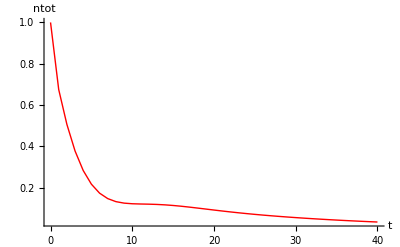

```mathematica
tmax=40;
n[0]=Table[If[i==1,1,0],{i,1,k}];

Do[
ntot[t]=Sum[n[t][[i]],{i,1,k}];
n[t+1]=a.n[t];
,{t,0,tmax}];

ListPlot[Table[{t,ntot[t]},{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{"t","ntot"}]

Animate[BarChart[n[t],PlotLabel->t],{t,0,tmax,1},AnimationRunning->False]
```

The population does not grow at a constant rate, but it looks like there might be a linear decrease.  The second plot shows the age distribution over time and we see that the second age group is the largest and it seems to develop quickly as the dominent one.

```mathematica
s=Outer[Times,v,w]/v.w;
s//MatrixForm

e=1/λ*s*a;
e//MatrixForm
```

(0.0579137 | 0.157259 | 0.0250904 | 0.00176836 | 0.00075708
0.0816439 | 0.221696 | 0.0353713 | 0.00249295 | 0.00106729
0.431812 | 1.17255 | 0.187078 | 0.0131851 | 0.00564489
6.69495 | 18.1795 | 2.90051 | 0.204426 | 0.0875201
25.1585 | 68.3155 | 10.8996 | 0.768201 | 0.328886)

The sensitivity matrix shows that lambda is most sensitive to the transition between the small juveniles (2) to adults (5), as seen with the 68.3155; however, the population matrix shows that this is not possible.

(0. | 0. | 0. | 0.00866916 | 0.0492446
0.0579137 | 0.163783 | 0. | 0. | 0.
0. | 0.0579137 | 0.129164 | 0. | 0.
0. | 0. | 0.0579137 | 0.146513 | 0.
0. | 0. | 0. | 0.0492446 | 0.279641)

The elasticity matrix shows that second stage to stay at the second stage contributes most to the population growth rate, with the highest value of 0.163783.

As stated in the paper, the most sensitive matrix parameters were surviving in one stage versus growth from one stage to another or reproductive output.

## Life history evolution

### Matrix models can be used to consider evolutionary pressure. In a density-independent setting like this, fitness=λ and natural selection would seek to maximize λ. Consider a trade-off between probability of maturing, x, and fecundity in the adult stage, assumed to be 10(1-x).

```mathematica
a={{0,10*(1-x)},{x,0}}

a//MatrixForm
```

{{0,10 (1-x)},{x,0}}

(0 | 10 (1-x)
x | 0)

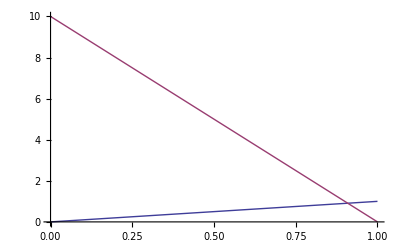

```mathematica
Plot[{x,10(1-x)},{x,0,1}]
```

```mathematica
Clear[x]
Solve[x==10(1-x)]
```

{{x→10/11}}

### What is the optimal life history strategy, x?

The optimal life history strategy is when x = 10/11, 0.9090.

```mathematica
Eigenvalues[a]
```

{-√10 √(x-x^2),√10 √(x-x^2)}

```mathematica
Solve[D[√10 √(x-x^2), x]=0, x][[x]]
```

Set::write: Tag D in ∂_x (√10\ √x - x^2) is Protected.

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Part::pspec: Part specification x is neither an integer nor a list of integers.

Solve[0,x]⟦x⟧

```mathematica
Solve[0,x]
```

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,x]

```mathematica
x=0.5
```

0.5

2

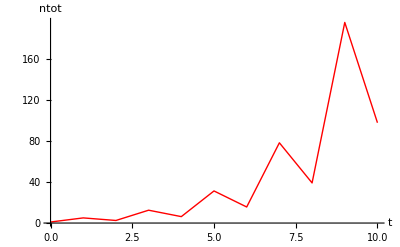

```mathematica
k=2
tmax=10;
n[0]={0,1};

Do[
ntot[t]=Sum[n[t][[i]],{i,1,k}];
n[t+1]=a.n[t];
,{t,0,tmax}];

ListPlot[Table[{t,ntot[t]},{t,0,tmax}],Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{"t","ntot"}]

Animate[BarChart[n[t],PlotLabel->t],{t,0,tmax,1},AnimationRunning->False]
```